# Вычисление влияния отклонения центрального электрода от оси внешнего цилиндрического электрода на конечный сигнал.

## Проверка формулы для электрического поля между некоаксиальными цилиндрами.

Основные формулы для вычисления конформного отображения.
a, b - параметры отображения
ρ - расстояние до центра проволочки
ϕ - угол

```mathematica
DD[r_, f_]:=a^2 + r^2  + 2a*r*Cos[f]
NN[r_,f_]:=Sqrt[(a+b*DD[r,f])^2+r^2+2(a+b*DD[r,f])*r*Cos[f]]
ρ[r_,f_]:=NN[r,f]/DD[r,f]
ϕ[r_,f_]:=ArcCos[(a+b*DD[r,f]+r*Cos[f])/NN[r,f]]
x[r_,f_]:= (a + r*Cos[f])/DD[r,f]+b
y[r_,f_]:= - r*Sin[f]/DD[r,f]
```

Параметры системы:
r0 - радиус внутренней проволоки
R0 - радиус внешнего цилиндра
δ -  смещение внутренней проволоки
все размерные величины выражены в микрометрах (μ)

```mathematica
r0 = 15
R0 = 2000
δ = 700
```

15

2000

700

Определение параметров a,b

```mathematica
b = N[2*δ*r0^2/(R0^2-r0^2-δ^2 + Sqrt[(R0^2 -(r0+δ)^2)(R0^2 - (r0-δ)^2)])]
a = b/(r0^2-b^2)
w1 =  R0/(R0^2-(δ+b)^2)
w2 = r0/(r0^2-b^2)
```

0.040341

0.000179295

0.000557647

0.0666671

Прорисовка эквипотенциальных поверхностей и линий напряжённости электрического поля.
rrE[angle] - рисует силовую линию 
ppU[r] - рисует эквипотенциальную поверхность

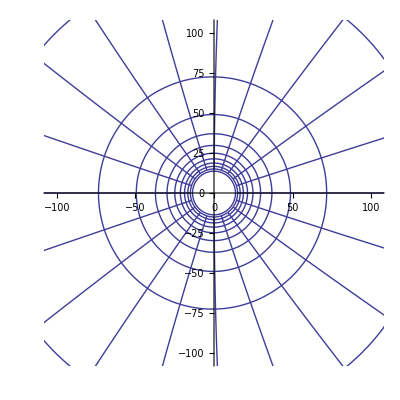

```mathematica
range ={{-1.3*(R0+0*δ)/25,1.3*(R0-0*δ)/25},{-1.3*R0/25,1.3*R0/25}};
ppE[angle_]:=ParametricPlot[{x[r,angle],y[r,angle]},{r,w1,w2},PlotRange->range, AspectRatio->1,DisplayFunction->Identity]
ppU[rr_]:=ParametricPlot[{x[rr, fi], y[rr,fi]},{fi,0, 2π}, PlotRange->range,AspectRatio->1,DisplayFunction->Identity]
Elines={};Ulines ={};
For[fi = 0, fi < 2π, fi = fi+ π/10;Elines = Append[Elines, ppE[fi]]];
For[rr = w1, rr <= w2, rr=rr+(w2-w1)/10; Ulines = Append[Ulines, ppU[rr]]];
Show[Union[Elines,Ulines],DisplayFunction->$DisplayFunction]
```

## Расчёт сигнала

```mathematica
SetParameters[dd_]:=Block[{},
r0 = 15; (* Радиус проволочки (μ) *)
R0 = 2000; (* Внутренний радиус трубки (μ) *)
δ = dd; (* Смещение проволочки
 (μ) *)
b = N[2*δ*r0^2/(R0^2-r0^2-δ^2 + Sqrt[(R0^2 -(r0+δ)^2)(R0^2 - (r0-δ)^2)])]; (* параметр конформного отображения (μ) *)
a = b/(r0^2-b^2); (* парамер конформного отображения(μ^-1) *)
w1 =  R0/(R0^2-(δ+b)^2); (* радиус внутреннего цилиндра праобраза конформного отображения (μ^-1) *)
w2 = r0/(r0^2-b^2); (* радиус внешнего цилиндра праобраза конформного отображения(μ^-1) *)
V=1325; (* напряжение между трубкой и проволочкой (В) *)
ϵ = 17.37; (* энергия ионизации (эВ)*)
L = 5.23 ; (* длина свободного пробега (μ) *)
]
```

### Длина пробега и начало ионизации.

Обратное отображение. Потенциал.

```mathematica
DDinv[r_, f_]:=b^2 + r^2  - 2b*r*Cos[f]
NNinv[r_,f_]:=Sqrt[(b+a*DD[r,f])^2+r^2-2(b+a*DD[r,f])*r*Cos[f]]
ρinv[r_,f_]:=NNinv[r,f]/DDinv[r,f]
ϕinv[r_,f_]:=ArcCos[-(b+a*DDinv[r,f]-r*Cos[f])/NNinv[r,f]]
U[rr_,ff_]:=V*Log[ρinv[rr,ff]/w1]/Log[w2/w1]
tr[u_]:=r0*(R0/r0)^(ϵ/u)/((R0/r0)^(ϵ/u)-1)
```

Разность потенциалов на длину свободного пробега.

```mathematica
ΔU[rr_,ff_]:=U[rr-L,ff]-U[rr,ff]
```

Rd - функция вычисляющая расстояние, с которого начинается лавинообразное рождение электронов, для данного угла.

```mathematica
Rd[ff_]:=(rx /. Evaluate[FindRoot[ΔU[rx,ff]==ϵ,{rx,65,90}]])
```

Таблица 
r - расстояние, с которого начинается лавинообразная ионизация.
V_eff - эффективное напряжение в коаксиальной системе, для которой расстояние начала лавинообразной ионизации равно r
U - потенциал на этом расстоянии

```mathematica
SetParameters[500]
For[ff=0,ff≤π,ff=ff+π/10; Print["ϕ = ",ff,"\t r = ",Rd[ff],"\t V_eff = ", ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)] ,"  U=", U[Rd[ff],ff]]]
```

ϕ = π/10	 r = 86.1814	 V_eff = 1357.53  U=842.272

ϕ = π/5	 r = 86.04	 V_eff = 1355.23  U=843.171

ϕ = (3 π)/10	 r = 85.8225	 V_eff = 1351.7  U=844.558

ϕ = (2 π)/5	 r = 85.5529	 V_eff = 1347.31  U=846.283

ϕ = π/2	 r = 85.2597	 V_eff = 1342.55  U=848.166

ϕ = (3 π)/5	 r = 84.9722	 V_eff = 1337.88  U=850.02

ϕ = (7 π)/10	 r = 84.7177	 V_eff = 1333.74  U=851.668

ϕ = (4 π)/5	 r = 84.5187	 V_eff = 1330.5  U=852.96

ϕ = (9 π)/10	 r = 84.3924	 V_eff = 1328.45  U=853.782

ϕ = π	 r = 84.3492	 V_eff = 1327.75  U=854.064

ϕ = (11 π)/10	 r = 84.3924	 V_eff = 1328.45  U=853.782

Фукция определяющая расстояние начала лавинообразной ионизации в зависимости от угла.

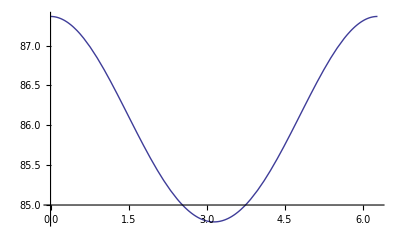

```mathematica
Plot[Rd[ff],{ff,0,2π}]
```

Зависимость номера канала от напряжения в коаксиальной системе, фит.

```mathematica
Y[x_]=(7.236496*10^(-5))*x^3-0.2710148*x^2+339.8670927*x-142617.2921796+142.15651
```

-142475.+339.867 x-0.271015 x^2+0.000072365 x^3

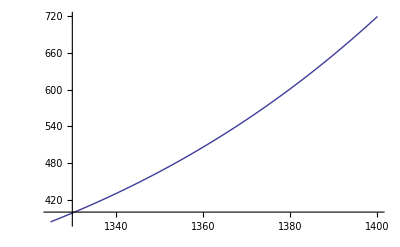

```mathematica
Plot[Y[x],{x,1325,1400}]
```

Распределение по номеру канала.

```mathematica
W1[u_,q_]:=NIntegrate[Exp[-(u-F[x])^2/(2*q^2*F[x]^2)]/(Sqrt[2π]*q*F[x]),{x,0,π}]/π
```

```mathematica
W[u_,q_]:=NIntegrate[Exp[-(u-F[x])^2/(2*q^2*F[x]^2)]/(Sqrt[2π]*q*F[x])*(Sqrt[R0^2-δ^2*Sin[x]^2]-δ*Cos[x]-r0)^2,{x,0,π}]/(π(R0^2-r0^2))
```

Нормировка на относительную погрешность Гауссова распределения.

```mathematica
q0=0.09/Sqrt[Log[2.]2]
```

0.076439

```mathematica
q0=0.12/Sqrt[Log[2.]2]
```

0.101919

Усреднённые распределения для различных отклонений проволочки.

```mathematica
SetParameters[0];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl1 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, DisplayFunction->Identity,PlotPoints->50];
SetParameters[200];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl2 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, PlotStyle->{Hue[0]}, DisplayFunction->Identity,PlotPoints->50];
SetParameters[400];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl3 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, PlotStyle->{Hue[0.2]}, DisplayFunction->Identity,PlotPoints->50];
SetParameters[600];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl4 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, PlotStyle->{Hue[0.4]}, DisplayFunction->Identity,PlotPoints->50];
SetParameters[800];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl5 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, PlotStyle->{Hue[0.6]}, DisplayFunction->Identity,PlotPoints->50];
SetParameters[1000];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl6 = Plot[{ W[u,q0]},{u,300,1000}, PlotRange->{Automatic,All}, PlotStyle->{Hue[0.8]}, DisplayFunction->Identity,PlotPoints->50];
Show[{pl1,pl2,pl3,pl4,pl5,pl6},Graphics[Text["   0μ", {900,0.012}, Background->RGBColor[0,0,0],TextStyle->{FontColor->RGBColor[1,1,1]}]],Graphics[Text[" 200μ", {900,0.0107}, Background->Hue[0],TextStyle->{FontColor->RGBColor[1,1,1]}]],Graphics[Text[" 400μ", {900,0.0094}, Background->Hue[0.2],TextStyle->{FontColor->RGBColor[0,0,0]}]],Graphics[Text[" 600μ", {900,0.0082}, Background->Hue[0.4],TextStyle->{FontColor->RGBColor[0.,0.,0.7]}]],Graphics[Text[" 800μ", {900,0.0069}, Background->Hue[0.6],TextStyle->{FontColor->RGBColor[1,1,1]}]],
Graphics[Text["1000μ", {900,0.0057}, Background->Hue[0.8],TextStyle->{FontColor->RGBColor[1,1,1]}]],DisplayFunction->$DisplayFunction];
```

Вычисление среднего номера канала по отклонению проволочки.

```mathematica
SetParameters[643];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
Print["Средний канал ", IntegerPart[N[NIntegrate[F[x]*(Sqrt[R0^2-δ^2*Sin[x]^2]-δ*Cos[x]-r0)^2,{x,0,π}]]/(π(R0^2-r0^2))]]
```

Средний канал 458

```mathematica
SetParameters[643];
Ftable=Table[{ff,Y[ϵ*Log[R0/r0]/Log[Rd[ff]/(Rd[ff]-L)]]},{ff,0,π,π/1000}];
F=Interpolation[Ftable];
pl1 = Plot[{55030* W[u,q0]},{u,0,650}, PlotRange->{Automatic,{0,700}},PlotPoints->50,AspectRatio->0.3];
```

```mathematica
ppE[angle_]:=ParametricPlot[{x[r,angle],y[r,angle]},{r,w1,w2},PlotRange->range, AspectRatio->1,DisplayFunction->Identity, PlotStyle->{Dotted,Black}]
ppU[rr_]:=ParametricPlot[{x[rr, fi], y[rr,fi]},{fi,0, 2π}, PlotRange->range,AspectRatio->1,DisplayFunction->Identity,PlotStyle->{Dotted,Black}]
Elines={};Ulines ={};
For[fi = 0, fi < 2π, fi = fi+ π/10;Elines = Append[Elines, ppE[fi]]];
For[rr = w1, rr <= w2, rr=rr+(w2-w1)/10; Ulines = Append[Ulines, ppU[rr]]];


hren := ParametricPlot[{Rd[fi]*Cos[fi], Rd[fi]*Sin[fi]},{fi,0, 2π}, PlotRange->range,AspectRatio->1,DisplayFunction->Identity, PlotStyle->{Orange}]
```

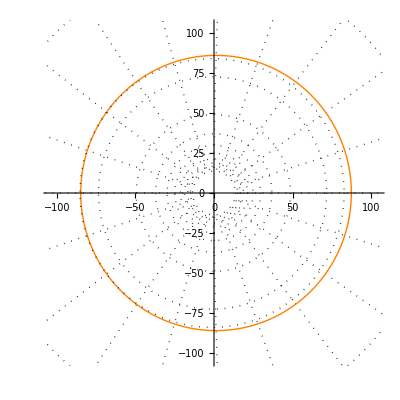

```mathematica
Show[Union[Elines,Ulines],hren,ppU[w2/5.6],DisplayFunction->$DisplayFunction]
```